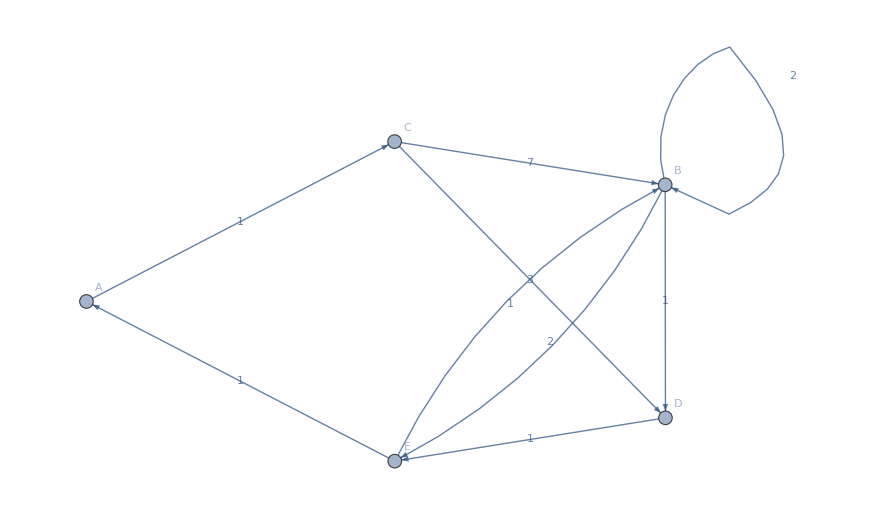

```mathematica
gr=ConstantArray[∞,{5,5}];
gr[[1,3]]=1;
gr[[2,2]]=2;
gr[[2,4]]=1;
gr[[2,5]]=2;
gr[[3,2]]=7;
gr[[3,4]]=3;
gr[[4,5]]=1;
gr[[5,1]]=1;
gr[[5,2]]=1;
WeightedAdjacencyGraph[gr,VertexLabels->{1->"A",2->"B",3->"C",4->"D",5->"E"},DirectedEdges->True,EdgeLabels->"EdgeWeight",EdgeLabelStyle->Large]
```

Notes:
Format for rectangle obj: {x,y,L,d}
{x,y} - lower left fill coordinate of rectangle (minimum coordinate is {1,1})
L - length of rectangle
d - type of rectangle (“h” - horizontal, “v” - vertical, “u” - unit square)
Solution rectangle to be specified as a solution function argument

```mathematica
getrectg[rect_,sol_:False]:=Block[{c1=rect[[1;;2]]-{1,1},c2=Switch[rect[[4]],"h",rect[[1;;2]]+{rect[[3]]-1,0},"v",rect[[1;;2]]+{0,rect[[3]]-1},"u",rect[[1;;2]]]},{If[sol,Red,Brown],EdgeForm[Directive[Thick,Black]],Rectangle[c1,c2],Directive[Thick,Black],Text["",(c1+c2)/2]}];
getrectgls[rectls_,sols_]:=Block[{ls=getrectg/@rectls,i},ls[[sols,1]]=Red;For[i=1,i≤Length[rectls],++i,ls[[i,-1,1]]=Style[ToString[i],Bold,Large]];Return[Join@@ls];];
getborder[gs_]:={Directive[Thick,Black],Line[{{0,0},{0,gs[[2]]},gs,{gs[[1]],0},{0,0}}]};
getcoords[gs_,srect_,s_]:=Switch[srect[[4]],"h",If[s==-1,{{0,srect[[2]]-1},{0,srect[[2]]}},{{gs[[1]],srect[[2]]-1},{gs[[1]],srect[[2]]}}],"v",If[s==-1,{{srect[[1]]-1,0},{srect[[1]],0}},{{srect[[1]]-1,gs[[2]]},{srect[[1]],gs[[2]]}}],"u",Print["ERROR: unit square for solution currently unsupported!"]];
showsystem[gs_,rinfo_,sols_]:=Block[{scoords=Table[getcoords[gs,rinfo[[sols[[i,1]]]],sols[[i,2]]],{i,Length[sols]}]},Graphics[Join[getborder[gs],getrectgls[rinfo,sols[[;;,1]]]],Epilog->(Style[Line[#],Thickness[0.015],Red]&/@scoords)]];
getoccupancymatrix[gs_,rinfo_]:=Block[{mat=ConstantArray[0,gs],i,t},For[i=1,i≤Length[rinfo],++i,t=rinfo[[i]];Switch[t[[4]],"h",mat[[t[[1]];;t[[1]]+t[[3]]-1,t[[2]]]]=1,"v",mat[[t[[1]],t[[2]];;t[[2]]+t[[3]]-1]]=1,"u",mat[[t[[1]],t[[2]]]]=1];];Return[mat];];
showoccupancy[occ_]:=MatrixPlot[Transpose@occ,DataReversed->{True,False}];
shiftrect[rect_,shift_]:={rect[[1]]+shift[[1]],rect[[2]]+shift[[2]],rect[[3]],rect[[4]]};
calcspace[arr_,asc_]:=Block[{i,n=Length[arr]},If[n==0,Return[0]];If[asc,For[i=1,i≤n,++i,If[arr[[i]]≠0,Return[i-1]]],For[i=n,i≥1,--i,If[arr[[i]]≠0,Return[n-i]]]];Return[n];];
FindMoves[rectls_,occ_]:=
(
Module[{gs,mvs,t,i,l,r,c,s},
gs=Dimensions[occ];
mvs={};
For[i=1,i≤Length[rectls],++i,
t=rectls[[i]];
Switch[t[[4]],"h",
(* Block with fixed y-value c, x-value [l,r] *)
c=t[[2]];
l=t[[1]];
r=l+t[[3]]-1;
(* Calculate space on the left *)
s=If[l>1,calcspace[occ[[1;;l-1,c]],False],0];
If[s>0,mvs=Append[mvs,{i,-s,0}];];
(* Calculate space on the right *)
s=If[r<gs[[1]],calcspace[occ[[r+1;;gs[[1]],c]],True],0];
If[s>0,mvs=Append[mvs,{i,s,0}];];
,"v",
(* Block with fixed x-value c, y-value [l,r] *)
c=t[[1]];
l=t[[2]];
r=l+t[[3]]-1;
(* Calculate space on the bottom *)
s=If[l>1,calcspace[occ[[c,1;;l-1]],False],0];
If[s>0,mvs=Append[mvs,{i,0,-s}];];
(* Calculate space on the top *)
s=If[r<gs[[2]],calcspace[occ[[c,r+1;;gs[[2]]]],True],0];
If[s>0,mvs=Append[mvs,{i,0,s}];];
,"u",
(* Unit block *)
c=t[[2]];
l=t[[1]];
(* Calculate space on the left *)
s=If[l>1,calcspace[occ[[1;;l-1,c]],False],0];
If[s>0,mvs=Append[mvs,{i,-s,0}];];
(* Calculate space on the right *)
s=If[r<gs[[1]],calcspace[occ[[l+1;;gs[[1]],c]],True],0];
If[s>0,mvs=Append[mvs,{i,s,0}];];
c=t[[1]];
l=t[[2]];
(* Calculate space on the bottom *)
s=If[l>1,calcspace[occ[[c,1;;l-1]],False],0];
If[s>0,mvs=Append[mvs,{i,0,-s}];];
(* Calculate space on the top *)
s=If[r<gs[[2]],calcspace[occ[[c,l+1;;gs[[2]]]],True],0];
If[s>0,mvs=Append[mvs,{i,0,s}];];
];
];
Return[mvs];
];
)
ApplyMove[rectls_,move_]:=Block[{res=rectls},res[[move[[1]],1;;2]]+=move[[2;;3]];Return[res];];
ApplyMovesNested[rectls_,moves_]:=Block[{res={rectls},i},For[i=1,i≤Length[moves],++i,res=Append[res,ApplyMove[res[[-1]],moves[[i]]]];];Return[res];];
SolutionQ[rectls_,sols_,occ_]:=Block[{gs=Dimensions[occ],i,t},For[i=1,i≤Length[sols],++i,t=rectls[[sols[[i,1]]]];Switch[t[[4]],"h",If[sols[[i,2]]==-1,If[calcspace[occ[[1;;t[[1]]-1,t[[2]]]],False]<t[[1]]-1,Return[False]],If[calcspace[occ[[t[[3]]+t[[1]];;gs[[1]],t[[2]]]],True]<gs[[1]]-t[[3]]-t[[1]]+1,Return[False]]],"v",If[sols[[i,2]]==-1,If[calcspace[occ[[t[[1]],1;;t[[2]]-1]],False]<t[[2]]-1,Return[False]],If[calcspace[occ[[t[[1]],t[[3]]+t[[2]];;gs[[2]]]],True]<gs[[2]]-t[[3]]-t[[2]]+1,Return[False]]],"u",Print["ERROR: unit square for solution currently unsupported!"]]];Return[True];];
GVAR={};
CT=0;
T1=0;T2=0;T3=0;T4=0;T5=0;
FindSolution[gs_,rinfo_,sols_,depth_Integer]:=FSRec[gs,rinfo,sols,{},depth,getoccupancymatrix[gs,rinfo]];
FSRec[gs_,rinfo_,sols_,mvlist_,depth_Integer,occmat_]:=
(
Module[{i,curmv,curmvs,mv,rnew,mvlsnew,occnew,t,tn},
CT=CT+1;
(* Check if given state is a solution - otherwise continue *)
T2+=Timing[If[SolutionQ[rinfo,sols,occmat],GVAR=mvlist;Return[True]];][[1]];
(* Check current depth - if still more than 0, continue *)
If[depth==0,Return[False]];
(* Calculate possible moves *)
T3+=Timing[curmvs=FindMoves[rinfo,occmat];][[1]];
(* Remove undesirable moves *)
(* Case 1 - Backward move *)
T4+=Timing[
If[Length[mvlist]>0,
mv=Last[mvlist];
mv[[2;;3]]=-mv[[2;;3]];
curmvs=DeleteCases[curmvs,mv];
];][[1]];
(* Loop through the new set of moves *)
For[i=1,i≤Length[curmvs],++i,
(* Update rectangle info and move list *)
mv=curmvs[[i]];
T5+=Timing[rnew=ApplyMove[rinfo,mv];
mvlsnew=Append[mvlist,mv];][[1]];
(* Update occupancy matrix *)
T1+=Timing[
t=rinfo[[mv[[1]]]];
tn=rnew[[mv[[1]]]];
occnew=occmat;
Switch[t[[4]],"h",occnew[[t[[1]];;t[[1]]+t[[3]]-1,t[[2]]]]=0;occnew[[tn[[1]];;tn[[1]]+tn[[3]]-1,tn[[2]]]]=1;,"v",occnew[[t[[1]],t[[2]];;t[[2]]+t[[3]]-1]]=0;occnew[[tn[[1]],tn[[2]];;tn[[2]]+tn[[3]]-1]]=1;,"u",occnew[[t[[1]],t[[2]]]]=0;occnew[[tn[[1]],tn[[2]]]]=1;];
][[1]];
If[FSRec[gs,rnew,sols,mvlsnew,depth-1,occnew],Return[True]];
];
Return[False];
];
)
```

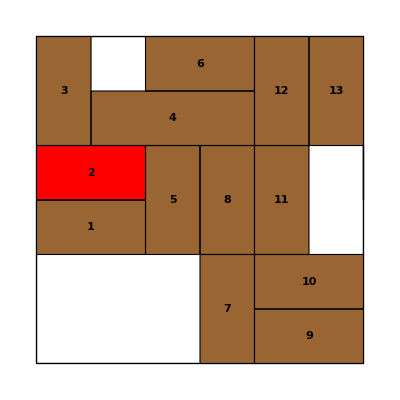

problemdef.dat

```mathematica
gs={6,6};
rinfo={
{1,3,2,"h"},
{1,4,2,"h"},
{1,5,2,"v"},
{2,5,3,"h"},
{3,3,2,"v"},
{3,6,2,"h"},
{4,1,2,"v"},
{4,3,2,"v"},
{5,1,2,"h"},
{5,2,2,"h"},
{5,3,2,"v"},
{5,5,2,"v"},
{6,5,2,"v"}
};
sols={{2,1}};
occmat=getoccupancymatrix[gs,rinfo];
showsystem[gs,rinfo,sols]
Export["problemdef.dat",Prepend[rinfo,{gs[[1]],gs[[2]],Length[rinfo],sols[[1,1]],sols[[1,1]]}]]
```

```mathematica
SetDirectory["C:\\My Pug's Stuff\\OneDrive\\Main repository\\WorkBunny\\Random LOLs\\unblockme\\unblockme"];
dat=Import["problemsol.dat"];
solmvs=dat[[2;;]];
state=showsystem[gs,#,sols]&/@ApplyMovesNested[rinfo,solmvs];
ListAnimate[state,AnimationRunning->False,AnimationRepetitions->1]
Export["unblockme_solution.gif",state,"DisplayDurations"->0.5]
```

unblockme_solution.gif

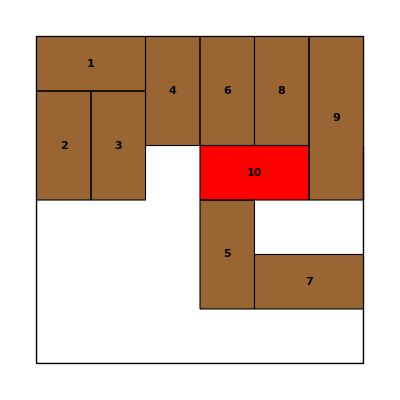

problemdef.dat

```mathematica
gs={6,6};
rinfo={
{1,6,2,"h"},
{1,4,2,"v"},
{2,4,2,"v"},
{3,5,2,"v"},
{4,2,2,"v"},
{4,5,2,"v"},
{5,2,2,"h"},
{5,5,2,"v"},
{6,4,3,"v"},
{4,4,2,"h"}
};
sols={{10,1}};
occmat=getoccupancymatrix[gs,rinfo];
showsystem[gs,rinfo,sols]
Export["problemdef.dat",Prepend[rinfo,{gs[[1]],gs[[2]],Length[rinfo],sols[[1,1]],sols[[1,1]]}]]
(*showoccupancy[occmat]
SolutionQ[rinfo,sols,occmat]*)
```

```mathematica
SetDirectory["C:\\My Pug's Stuff\\OneDrive\\Main repository\\WorkBunny\\Random LOLs\\unblockme\\unblockme"];
dat=Import["problemsol.dat"];
solmvs=dat[[2;;]];
state=showsystem[gs,#,sols]&/@ApplyMovesNested[rinfo,solmvs];
ListAnimate[state,AnimationRunning->False,AnimationRepetitions->1]
Export["unblockme_solution.gif",state,"DisplayDurations"->0.5]
```

unblockme_solution.gif

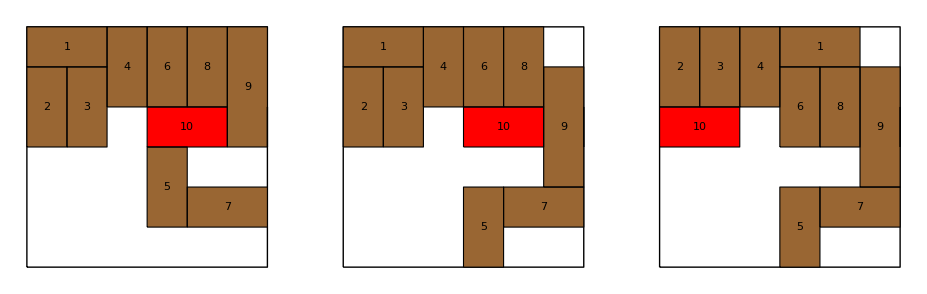

```mathematica
rtest={
{0,5,2,"h"},
{0,3,2,"v"},
{1,3,2,"v"},
{2,4,2,"v"},
{3,0,2,"v"},
{3,4,2,"v"},
{4,1,2,"h"},
{4,4,2,"v"},
{5,2,3,"v"},
{3,3,2,"h"}
};
rtest2={
{3,5,2,"h"},
{0,4,2,"v"},
{1,4,2,"v"},
{2,4,2,"v"},
{3,0,2,"v"},
{3,3,2,"v"},
{4,1,2,"h"},
{4,3,2,"v"},
{5,2,3,"v"},
{0,3,2,"h"}
};
rtest[[;;,{1,2}]]+=1;
rtest2[[;;,{1,2}]]+=1;
GraphicsRow[{showsystem[gs,rinfo,sols],showsystem[gs,rtest,sols],showsystem[gs,rtest2,sols]}]
```

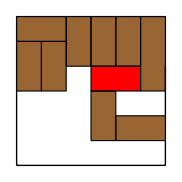

(2 | 0 | -3
3 | 0 | -3
4 | 0 | -4
5 | 0 | -1
9 | 0 | -1
10 | -1 | 0)

({1,6,2,h} | {1,1,2,v} | {2,4,2,v} | {3,5,2,v} | {4,2,2,v} | {4,5,2,v} | {5,2,2,h} | {5,5,2,v} | {6,4,3,v} | {4,4,2,h}
{1,6,2,h} | {1,4,2,v} | {2,1,2,v} | {3,5,2,v} | {4,2,2,v} | {4,5,2,v} | {5,2,2,h} | {5,5,2,v} | {6,4,3,v} | {4,4,2,h}
{1,6,2,h} | {1,4,2,v} | {2,4,2,v} | {3,1,2,v} | {4,2,2,v} | {4,5,2,v} | {5,2,2,h} | {5,5,2,v} | {6,4,3,v} | {4,4,2,h}
{1,6,2,h} | {1,4,2,v} | {2,4,2,v} | {3,5,2,v} | {4,1,2,v} | {4,5,2,v} | {5,2,2,h} | {5,5,2,v} | {6,4,3,v} | {4,4,2,h}
{1,6,2,h} | {1,4,2,v} | {2,4,2,v} | {3,5,2,v} | {4,2,2,v} | {4,5,2,v} | {5,2,2,h} | {5,5,2,v} | {6,3,3,v} | {4,4,2,h}
{1,6,2,h} | {1,4,2,v} | {2,4,2,v} | {3,5,2,v} | {4,2,2,v} | {4,5,2,v} | {5,2,2,h} | {5,5,2,v} | {6,4,3,v} | {3,4,2,h})

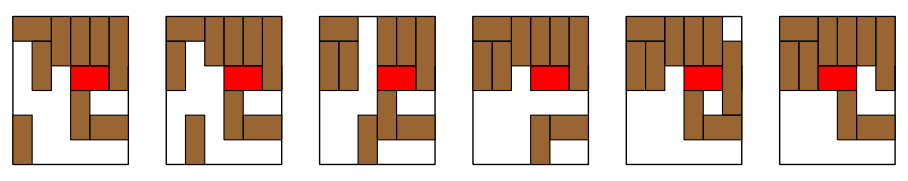

{True,True,True,True,True,True}

```mathematica
showsystem[gs,rinfo,sols]
FindMoves[rinfo,occmat]
ApplyMove[rinfo,#]&/@%
GraphicsRow@(showsystem[gs,#,sols]&/@%)
SolutionQ[#,sols,getoccupancymatrix[gs,#]]&/@%%
```